449 Midterm
Megan Tabbutt
4/6/18

```mathematica
Import["/Users/megantabbutt/Desktop/Quantum/Defs/448defs.m"]
```

Each problem is worth the same. The usual take-home rules apply, in particular no discussing this with any other humans. Due 8 am Friday April 6. Hand in electronically, maximum of one .nb and one pdf file. I reserve the right to deduct points for answers that are difficult to read.

## 1) Sr has 2 valence electrons. Some of its important low-lying excited states are denoted 5s 5p ^3 P_j.

a) What are the possible values of j?

^3 P_j = ^(2S+1)L_j 	--> 	S = 1,   L = 1 

J = L + S 			-->	 Addition of Ang Mom: 			j = 0, 1, 2. 

(Citation: Townsend Ch 3)

The possible values of j: 	     j = 0, 1, 2.

b) Let your largest answer to a) be j_max. Assuming the radial wavefunctions are P_(5s)(r) and P_(5p)(r), write down the total wavefunction for the state with j = m = j_max.

j_max = 2 . 			j = m = j_max 	 j = L + S, 			j = 2,  m=2,  L = 1,   S = 1

Individual Wavefunctions for the electrons is given by: 		ψ(r, θ, ϕ)=(P(r))/r Σ_(m_l m_s)C_(L m_l Sm_s)^(J m)Y_(L m_l)(θ,ϕ)m_s
The total wave function is given by: 	ψ_total =( Σ_(m_l m_s)C_(L m_l Sm_s)^(J m) )ψ_1 ψ_2 χ_ms   , 		where now the CG coefficient is for the total QM# 

The Clebsch-Gordon Coefficients are given by:	 Σ_(m_l m_s)C_(L m_l Sm_s)^(J m)  = Σ_(m_l m_s)C_(1 m_l 1 m_s)^(2 2) 	Because of selection rules, the only nonzero CG is the C_(1 111)^(2 2) . Selection Rules: 	m = ml + ms = 2. 	L = 1  -->   ml = -1, 0, 1 	Similarly, 		S = 1  -->   ms = -1, 0, 1 	Thus, ml and ms have to both be 1 to satisfy the condition on m. This is also apparent from the fact that we have chosen the maximal J and mj states, so there is only one combination of ml and ms to get this. 

ψ_1 and ψ_2 are the individual wavefunctions for the elections given by:

ψ_1(r_1, θ_1, ϕ_1)=(P_(5s)(r_1))/r_1 Y_(L_1 m_l_1)(θ_1,ϕ_1) = ψ_1(r_1, θ_1, ϕ_1)=(P_(5s)(r_1))/r_1 Y_(0 0)(θ_1,ϕ_1)
ψ_2(r_2, θ_2, ϕ_2)=(P_(5p)(r_2))/r_2 Y_(L_2 m_l_2)(θ_2,ϕ_2) = ψ_2(r_2, θ_2, ϕ_2)=(P_(5p)(r_2))/r_2 Y_(1 1)(θ_2,ϕ_2)

ψ_total =( Σ_(m_l m_s)C_(L m_l Sm_s)^(J m) )ψ_1 ψ_2 χ_ms   = 	C_(1 111)^(2 2) (P_(5s)(r_1))/r_1 Y_(0 0)(θ_1,ϕ_1)(P_(5p)(r_2))/r_2 Y_(1 1)(θ_2,ϕ_2) χ_ms = 1(P_(5s)(r_1))/r_1 Y_(0 0)(θ_1,ϕ_1)(P_(5p)(r_2))/r_2 Y_(1 1)(θ_2,ϕ_2))χ_1

ψ_total = ((P_(5s)(r_1))/r_1 Y_00(θ_1,ϕ_1))((P_(5p)(r_2))/r_2 Y_11(θ_2,ϕ_2)) χ_1

(Citation: Prof Walker’s Atomic State Notebook)

ψ_total = ((P_(5s)(r_1))/r_1 Y_00(θ_1,ϕ_1))((P_(5p)(r_2))/r_2 Y_11(θ_2,ϕ_2)) χ_1

c) Simplify: 5s 5p  ^3 P_jmax 1/r_12 5s 5p  ^3 P_jmax=

5s 5p  ^3 P_jmax 1/r_12 5s 5p  ^3 P_jmax=  ∫_0^∞ ∫_0^∞ ((P_(5s)(r_1))/r_1)^2 1/r_12((P_(5p)(r_2))/r_2)^2 r_1^2 r_2^2 ⅆ r_1ⅆ r_2∫_0^π ∫_0^(2 π) (Y_00(θ_1,ϕ_1))^2 Sin[θ_1]ⅆ θ_1ⅆ ϕ_1∫_0^π ∫_0^(2 π) (Y_11(θ_2,ϕ_2))^2 Sin[θ_2]ⅆ θ_2ⅆ ϕ_2
 
 ∫_0^π ∫_0^(2 π) (Y_00(θ_1,ϕ_1))^2 Sin[θ_1]ⅆ θ_1ⅆ ϕ_1 = 1
 
 
 
 (Citation: Prof Walker’s H21s2s Notebook and Townsend 9.9)

```mathematica
Angular1 = Integrate[(SphericalHarmonicY[0, 0, Subscript[θ, 1], Subscript[ϕ, 1]])^2 Sin[Subscript[θ, 1]], {Subscript[θ, 1],0,π}, {Subscript[ϕ, 1],0,2 π}]
```

1

```mathematica
SphericalHarmonicY[1, 1, Subscript[θ, 2], Subscript[ϕ, 2]]
Angular2 = Integrate[(SphericalHarmonicY[1, 1, Subscript[θ, 2], Subscript[ϕ, 2]])^2 Sin[Subscript[θ, 2]], {Subscript[θ, 2],0,π}, {Subscript[ϕ, 2],0,2 π}]
```

-1/2 ⅇ^(ⅈ ϕ_2) √(3/(2 π)) Sin[θ_2]

0

```mathematica
∫_0^∞ ∫_0^∞ ((Subscript[P, 5s](Subscript[r, 1]))/Subscript[r, 1])^2 1/Subscript[r, 12]((Subscript[P, 5p](Subscript[r, 2]))/Subscript[r, 2])^2 Subscript[r, 1]^2 Subscript[r, 2]^2 ⅆ Subscript[r, 1]ⅆ Subscript[r, 2]∫_0^π ∫_0^(2 π) (Subscript[Y, 00](Subscript[θ, 1],Subscript[ϕ, 1]))^2 Sin[Subscript[θ, 1]]ⅆ Subscript[θ, 1]ⅆ Subscript[ϕ, 1]∫_0^π ∫_0^(2 π) (Subscript[Y, 11](Subscript[θ, 2],Subscript[ϕ, 2]))^2 Sin[Subscript[θ, 2]]ⅆ Subscript[θ, 2]ⅆ Subscript[ϕ, 2]
```

```mathematica
Subscript[P, n_, l_][r_, Z_]:=√Z*Subscript[P, n, l][Z*r];
```

```mathematica
Subscript[P, 5, 0][Subscript[r, 1], 2]
```

(ⅇ^(-(2 r_1)/5) r_1 (120-192 r_1+(384 r_1^2)/5-(256 r_1^3)/25+(256 r_1^4)/625))/(75 √10)

```mathematica
Subscript[P, 5, 1][Subscript[r, 2], 2]
```

(4 ⅇ^(-(2 r_2)/5) r_2^2 (-120+72 r_2-(288 r_2^2)/25+(64 r_2^3)/125))/(375 √15)

```mathematica
Integrate[Subscript[P, 5, 0][Subscript[r, 1], 2]Subscript[P, 5, 0][Subscript[r, 1], 2]Min[1/Subscript[r, 2],1/Subscript[r, 1]]Subscript[P, 5, 1][Subscript[r, 2], 2]Subscript[P, 5, 1][Subscript[r, 2], 2],{Subscript[r, 2],0,∞},{Subscript[r, 1],0,∞}]
```

19781/409600

## 2) A spin-0 particle with charge q = | e | and mass M moves in the spherically symmetric potential V(r) =  0 | r<a ∞ | r>a. The energy levels can be parameterized by the equation E_nl = (π^2 ℏ^2)/(2 M a^2)(n + δ_l)^2, where n is the number of radial zero crossings and δ_l depends, to a good approximation, mostly on l but only slightly on n.)

a) For s-states, the equation is exact. What is the value of δ for s-states?

s states have l = 0 

For a spherical potential we have that the solutions are spherical Bessel functions. Energy eigenvalues are determined by: j_l(k a)=0. (Townsend 10.70). Thus for the s states, where l = 0, we need the zeroth spherical Bessel function to be zero at a, and so we  need to find the first zero of the zeroth spherical Bessel function.

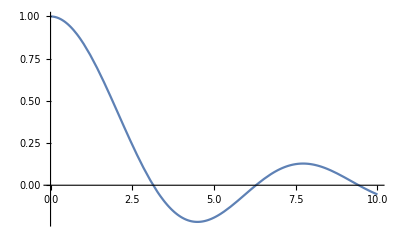

```mathematica
Plot[SphericalBesselJ[0, x], {x, 0, 10}]
```

```mathematica
FindRoot[SphericalBesselJ[0, x], {x, 2, 4}]
```

{x→3.14159}

The first zero of the zeroth Spherical Bessel Function is  at x = π. 

j_0(k r) = 0 = Sin[k r]/(k r), 	but x = k r = pi to satisfy this , 	in fact k r = n π will satisfy this equation. 	

Following a similar procedure to 10.4: 	k = Sqrt[(2 M E)/ℏ^2]  -- > 	E = (ℏ^2 k^2)/(2 M)

But we just found for the l = 0 case: 	k = (n π)/r

Thus for the s states:  	E_n0 = ℏ^2/(2 M)((π^2 n^2)/r^2),    r = a,  so we know that  E_n0 = ℏ^2/(2 M)((π^2 n^2)/a^2).

We want to find the value of δ_(l=0) though, so we need to solve these two equations: 	E_(nl=0) = (π^2 ℏ^2)/(2 M a^2)(n + δ_l)^2 = ℏ^2/(2 M)((π^2 n^2)/a^2). 

Clearly δ_l = 0.

(Citation: Townsend 10.4 and Griffiths example 4.1)

So we can see that δ_l = 0  for the s states.

b) Put δ0, δ1, and δ2 in numerical order. Briefly explain your reasoning.

```mathematica
Subscript[E, n0] = ℏ^2/(2 M)((π^2 n^2)/a^2)

Subscript[E, nl] = (π^2 ℏ^2)/(2 M a^2)(n + Subscript[δ, l])^2 

Subscript[j, 0](r) = 0 = Sin[r]/r
```

c) A magnetic field is applied, of strength B. Find the first-order correction to the energy levels.

d) Two more identical particles are added. What is the energy and degeneracy of the first excited state for B = 0?

## 4)

What is || 2 s d; 1 s u; 2 s u||(Ŝ)^2|| 2 s d; 1 s u; 2 s u||, where S̄ = OverBar[S_1]  + OverBar[S_2]  + OverBar[S_3]  is the total spin opera-
tor of the 3 electrons in the Li atom? You can probably figure out the answer from the NIST tables, but use your knowledge of Li wavefunctions and spin operators to prove it.

|| 2 s d; 1 s u; 2 s u||(Ŝ)^2|| 2 s d; 1 s u; 2 s u||, S̄ = OverBar[S_1]  + OverBar[S_2]  + OverBar[S_3]  

(Citation: )

```mathematica
|| 2 s d; 1 s u; 2 s u||(Ŝ)^2|| 2 s d; 1 s u; 2 s u||
S̄ = OverBar[Subscript[S, 1]]  + OverBar[Subscript[S, 2]]  + OverBar[Subscript[S, 3]]
```

|| 2 s d; 1 s u; 2 s u||(Ŝ)^2|| 2 s d; 1 s u; 2 s u|| =